```mathematica
(*
eps = e-2, e-6, e-17

[0; 1]

Begin
R1:=Exp((Degree(x,4)+2*Degree(x,3)-5*x+6)/5);
R2:=Coh(1/(-15*Degree(x,3)+10*x+5*Sqrt(10)));
VarF:=R1+R2-3;
End;
*)
$MinPrecision=20;
```

```mathematica
F[x_]:=Exp[(x^4+2 * x^3 - 5*x+6)]+
Cosh[1/(-15*x^3+10*x+5*Sqrt[10])]-3;
Dexot[precision_]:=Module[{graphValues, NonGraphValues},
eps = 10^-precision;
delta = eps*10^-4;
leftBound = 0;
rightBound = 1;
nextLeftBound[a_, b_]:=(a+b)/2-delta;
nextRightBound[a_, b_]:=(a+b)/2+delta;
IterationCountrer = 0;

graphValues=List[];
NonGraphValues=List[];
While[(rightBound -leftBound) > eps/10,
nextLeft = nextLeftBound[leftBound, rightBound];
nextRight = nextRightBound[leftBound, rightBound];
leftFunc = F[nextLeft];
rightFunc = F[nextRight];
If[leftFunc <= rightFunc,
rightBound=nextRight;
AppendTo[graphValues, {rightBound, rightFunc}];
AppendTo[NonGraphValues, {nextLeft, leftFunc}];
,
leftBound = nextLeft;
AppendTo[graphValues, {nextLeft, leftFunc}];
AppendTo[NonGraphValues, {rightBound, rightFunc}];
] ;
++IterationCountrer;
];

Subscript[x, min]=SetPrecision[(rightBound+leftBound)/2,20];
Subscript[y, min]=SetPrecision[F[Subscript[x, min]],20];
Print["Answer: ",Subscript[y, min],"\nIterations: ", IterationCountrer, "\nFunction calculations: ", IterationCountrer * 2, "\nPrecition: ", precision, "\nx_min = ",Subscript[x, min] ];
(*Return[SetPrecision[N[F[rightBound-leftBound]],20]];*)
Return[
Show[Plot[F[x], {x, 0.4, 1.1}, PlotRange->{{0.4, 1.1},{0,80}}],
ListPlot[{ graphValues,NonGraphValues},PlotStyle->{Red, Green},PlotLegends->{"included in calculations","excluded from calculations"}],
ListPlot[{{Subscript[x, min], Subscript[y, min]}}, PlotStyle->{Black},PlotLegends->{"minimum"} ],
AxesLabel->{"x","y"}
]
];
];
```

Answer: 28.267971145878340365
Iterations: 10
Function calculations: 20
Precition: 2
x_min = 0.7456049775390625

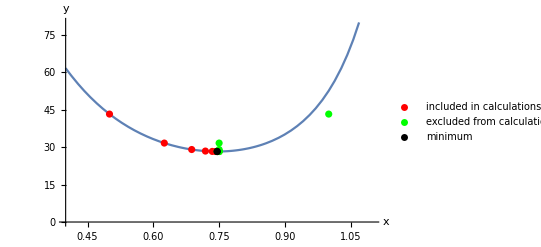

```mathematica
Dexot[2]
```

Answer: 28.267932308726998627
Iterations: 24
Function calculations: 48
Precition: 6
x_min = 0.74601021404114524722

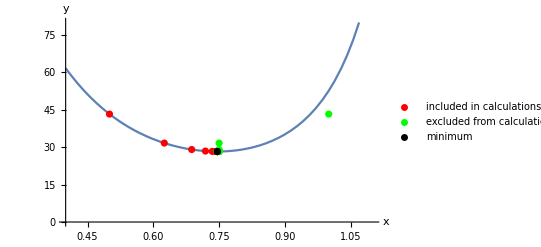

```mathematica
Dexot[6]
```

Answer: 28.267932308726974821
Iterations: 60
Function calculations: 120
Precition: 17
x_min = 0.74601022407293917467

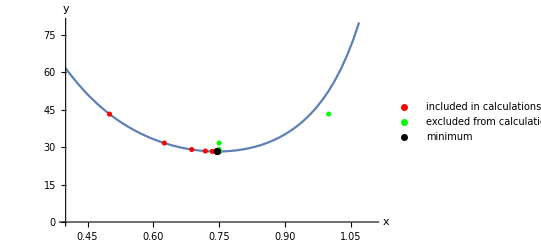

```mathematica
Dexot[17]
```

```mathematica
GoldenRat[precision_]:=Module[{},
eps = 10^-precision;
leftBound = 0;
rightBound = 1;
goldenRat = (1+Sqrt[5])/2;
nextLeftBound[a_, b_]:=a+(b-a)/(goldenRat+1);
nextRightBound[a_, b_]:=b-(b-a)/(goldenRat+1);
leftFunc = F[leftBound];
rightFunc = F[rightBound];

nextLeft = nextLeftBound[leftBound, rightBound];
nextRight=leftBound+rightBound-nextLeft;

If[nextRight<nextLeft,
temp= nextLeft;
nextLeft = nextRight;
nextRight = temp;,];

nextLeftFunc = F[nextLeft];
nextRightFunc = F[nextRight];
next = 0;nextF = 0;

If[nextLeftFunc <= nextRightFunc,
rightBound=nextRight;
next = nextLeft;
nextF = nextLeftFunc;
graphValues={{rightBound, nextRightFunc}};
NonGraphValues={{next, nextF}};
,
leftBound = nextLeft;
next = nextRight;
nextF = nextRightFunc;
graphValues={{rightBound, nextRightFunc}};
NonGraphValues={{next, nextF}};
] ;
IterationCountrer = 1;

While[(rightBound -leftBound) > eps/10,
nextNew=leftBound+rightBound-next;
nextNewF = F[nextNew];
If[nextNew <= next, 
nextLeft = nextNew;
leftFunc= nextNewF;
nextRight = next;
rightFunc = nextF;
,
nextLeft = next;
leftFunc= nextF;
nextRight = nextNew;
rightFunc = nextNewF;
];

If[leftFunc <= rightFunc,
rightBound=nextRight;
next = nextLeft;
nextF = nextLeftFunc;
AppendTo[graphValues,{nextRight, rightFunc}];
AppendTo[NonGraphValues,{next, nextF}];
,
leftBound = nextLeft;
next = nextRight;
nextF = nextRightFunc;
AppendTo[graphValues,{nextLeft, leftFunc}];
AppendTo[NonGraphValues,{next, nextF}];
] ;

++IterationCountrer;
];

Subscript[x, min]=SetPrecision[(rightBound+leftBound)/2,20];
Subscript[y, min]=SetPrecision[F[Subscript[x, min]],20];
Print["Answer: ",Subscript[y, min],"\nIterations: ", IterationCountrer, "\nFunction calculations: ", IterationCountrer +1, "\nPrecition: ", precision, "\nx_min = ",Subscript[x, min] ];

Return[
Show[Plot[F[x], {x, 0.4, 1.1}, PlotRange->{{0.4, 1.1},{0,80}}],
ListPlot[{ graphValues,NonGraphValues},PlotStyle->{Red, Green},PlotLegends->{"included in calculations","excluded from calculations"}],
ListPlot[{{Subscript[x, min], Subscript[y, min]}}, PlotStyle->{Black},PlotLegends->{"minimum"} ],
AxesLabel->{"x","y"}
]
];
];
```

Answer: 28.348081486406981017
Iterations: 15
Function calculations: 16
Precition: 2
x_min = 0.76429859121813900599

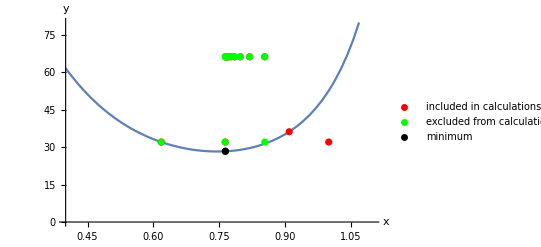

```mathematica
GoldenRat[2]
```

Answer: 28.34487905857801659
Iterations: 34
Function calculations: 35
Precition: 6
x_min = 0.76393206170961384779

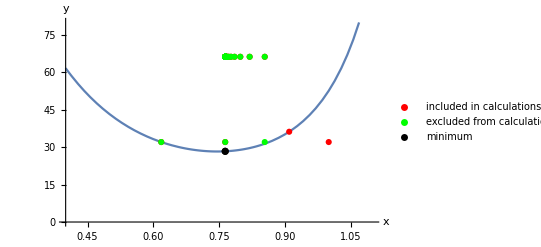

```mathematica
GoldenRat[6]
```

Answer: 28.344878719544231442
Iterations: 87
Function calculations: 88
Precition: 17
x_min = 0.76393202250021030391

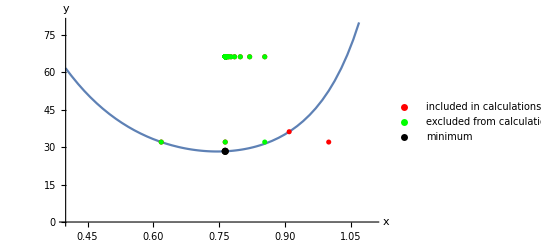

```mathematica
GoldenRat[17]
```

```mathematica
(*
Вывод

Ни один из методов не дает точный ответ, так как результат получается сравнением значений функции в конечном числе точек.

Из результатов работы программ следует, что метод золотого сечения эффективнее, чем метод дихотомии. Совершается меньше вычислений функций и итераций. Теоретический материал учебника "Введение в методы оптимизации" (А.В.Аттеков и др.) подтверждает это.
*)
```